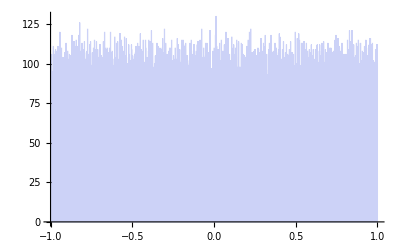

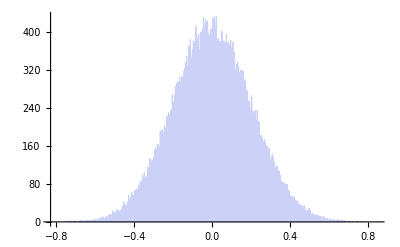

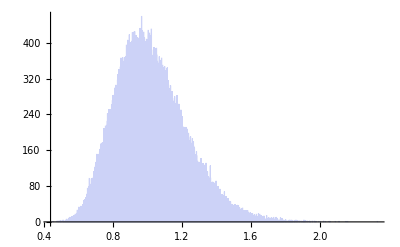

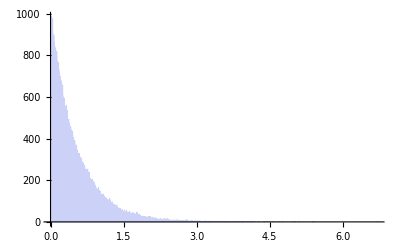

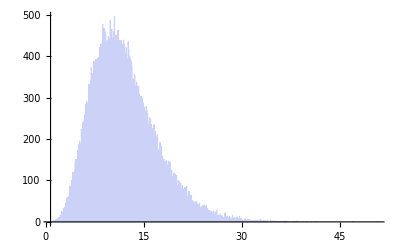

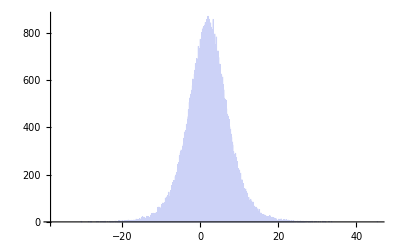

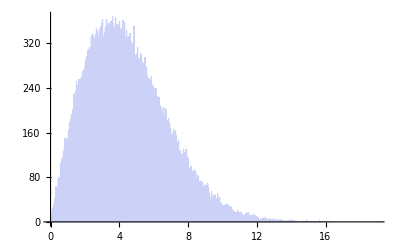

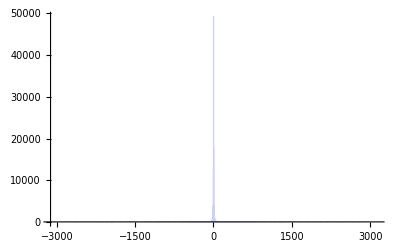

```mathematica
root=NotebookDirectory[];
uniform=Import[root<>"uniform.txt","List"];
normal=Import[root<>"normal.txt","List"];
lognormal=Import[root<>"lognormal.txt","List"];
exponential=Import[root<>"exponential.txt","List"];
gamma=Import[root<>"gamma.txt","List"];
logistic=Import[root<>"logistic.txt","List"];
VeibullGnedenko=Import[root<>"Veibulla-Gnedenko.txt","List"];
cauchy=Import[root<>"cauchy.txt","List"];
chisquare=Import[root<>"chisquare.txt","List"];
student=Import[root<>"student.txt","List"];


Histogram[uniform,1000]
Histogram[normal,1000]
Histogram[lognormal,1000]
Histogram[exponential,1000]
Histogram[gamma,1000]
Histogram[logistic,1000]
Histogram[VeibullGnedenko,1000]
Histogram[cauchy,1000]
Histogram[chisquare,1000]
Histogram[student,1000]
```